# Single-shot Readout for Superconducting Qubit w/ Two-tone Readout & Shelving Techniques for Quantum Computing

```mathematica
myred=ColorData[97][4];myblue=ColorData[97][1];myorange=ColorData[97][2];mygreen=ColorData[97][3];
dataPath="https://raw.githubusercontent.com/muxueqianxun/SuperconductingQubitReadout/main/ReadoutData/";
fontsize=14;font="CMU Sans Serif";
SetOptions[EvaluationNotebook[],StyleDefinitions->Cell[StyleData["GraphicsLabel"],Black,fontsize,FontFamily->font]];
```

## Readout Response

### Import VNA Data

```mathematica
dataPathCalib=dataPath<>"Calibration/";
dataVNAName=dataPathCalib<>"VNAZoom1.hdf5";
```

```mathematica
dataVNA=Import[dataVNAName,"/Traces/VNA - S21"];
VNASignalWide=AbsArg[(dataVNAᵀ⟦1⟧)ᵀ⟦-2⟧+I*(dataVNAᵀ⟦2⟧)ᵀ⟦-2⟧];
dataVNAStart=Import[dataVNAName,"/Step config/VNA - Start frequency/Step items"]⟦1⟧["single"];
dataVNAStop=Import[dataVNAName,"/Step config/VNA - Stop frequency/Step items"]⟦1⟧["single"];
dataVNAStep=Import[dataVNAName,"/Step config/VNA - # of points/Step items"]⟦1⟧["single"];
```

```mathematica
freqSweep=Range[dataVNAStart,dataVNAStop,Abs[(dataVNAStop-dataVNAStart)]/(dataVNAStep-1)];
dataPhase=VNASignalWide⟦All,2⟧;
cut=Round[0.59*dataVNAStep];cut1=Round[0.2*dataVNAStep];
dataVNA = {freqSweep/10^9,20*Log10[VNASignalWide⟦All,1⟧]}ᵀ;
dataVNASmooth=MovingAverage[dataVNA,2000];
```

### Purcell Filter

```mathematica
bSol=Solve[0==-I*Δ*b-κf/2*b-I*ϵf(*-γb*b*),b]⟦1⟧;
```

```mathematica
modelf=Simplify[20*Log10[κf^2/4*b*Conjugate[b]/.bSol⟦1⟧/.{Δ->f-ωp}],{ϵf∈Reals,f∈Reals,κf∈Reals,γb∈Reals,ωp∈Reals}];
```

```mathematica
cut=Round[0.75*dataVNAStep];cut1=Round[0.35*dataVNAStep];cut2=Round[0.56*dataVNAStep];
cut3=Round[0.78*dataVNAStep];
dataVNASmoothCut = dataVNASmooth⟦cut1;;cut2⟧;
dataVNASmoothCut1 = dataVNASmooth⟦cut;;-1⟧;
dataVNASmoothCutL=dataVNASmooth⟦cut1;;cut3⟧;
dataVNASmoothCut2=Join[dataVNASmoothCut,dataVNASmoothCut1];
```

```mathematica
resultf=NonlinearModelFit[dataVNASmoothCutL,modelf,{{ωp, 6.5},{κf,0.4}(*,{γb,0}*),{ϵf,1}},f,MaxIterations->1000];
```

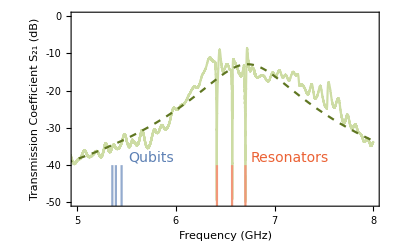

```mathematica
imsize=395;
qbList={5.357555,5.35755,5.39357,5.39357,5.45141,5.45141};
roList={6.45311,6.45311,6.60611,6.60611,6.74131,6.74131}-0.036;
line={-40,-60,-40,-60,-40,-60};
qubitline=Partition[{qbList,line}ᵀ,2];
roline=Partition[{roList,line}ᵀ,2];
fitplotf=Legended[Show[ListPlot[{dataVNA},Joined->True,PlotRange->{{5,8},{0,-50}},GridLines->Automatic,Frame->True,ImageSize->imsize,FrameTicks-> {{Range[-50,0,10],None},{Range[5,8,0.5]/.{5.-> 5,6.-> 6,7.-> 7,8.-> 8},None}},PlotStyle->{{Lighter[Lighter[mygreen]],Thickness[0.004]}},FrameLabel->{"Frequency (GHz)","Transmission Coefficient S_21 (dB)"},Epilog->{{Text[Style["Qubits",fontsize,myblue,FontFamily->font],{5.75,-38}]},{Text[Style["Resonators",fontsize,myred,FontFamily->font],{7.15,-38}]}},ImageMargins-> 0],ListPlot[qubitline,Joined->True,PlotStyle->{Lighter[myblue]}],
ListPlot[roline,Joined->True,PlotStyle->{Lighter[myred]}],Plot[resultf[f],{f,dataVNA⟦1,1⟧,dataVNA⟦-1,1⟧},PlotStyle-> {Darker[mygreen],Dashed}]],Placed[Framed[LineLegend[{Lighter[Lighter[mygreen]],{Darker[mygreen],Dashed}},{"Data","Fit"},LabelStyle->{FontFamily->font}],Background-> White,FrameMargins->0.1],{Left,Top}]]
```

## Resonator 2 Zoom-in

### Import Data

```mathematica
dataRQA=Import[dataPathCalib<>"Q1Q2Q3SSRO123pulseROSweep_3.hdf5","/Data/Data"];
r1sweep=dataRQA⟦All,3,1⟧*10^-9;
r2sweep=dataRQA⟦All,4,1⟧*10^-9;
r3sweep=dataRQA⟦All,5,1⟧*10^-9;
```

```mathematica
r1g=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-6;;-5⟧]⟦1;;;;4⟧,2];r1e=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-6;;-5⟧]⟦2;;;;4⟧,2];
r1f=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-6;;-5⟧]⟦3;;;;4⟧,2];
r1h=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-6;;-5⟧]⟦4;;;;4⟧,2];
r2g=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-4;;-3⟧]⟦1;;;;4⟧,2];
r2e=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-4;;-3⟧]⟦2;;;;4⟧,2];
r2f=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-4;;-3⟧]⟦3;;;;4⟧,2];
r2f=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-4;;-3⟧]⟦3;;;;4⟧,2];
r2h=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-4;;-3⟧]⟦4;;;;4⟧,2];
r3g=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-2;;-1⟧]⟦1;;;;4⟧,2];
r3e=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-2;;-1⟧]⟦2;;;;4⟧,2];
r3f=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-2;;-1⟧]⟦3;;;;4⟧,2];
r3h=#⟦1⟧+I*#⟦2⟧&/@Partition[Flatten[dataRQA⟦All,-2;;-1⟧]⟦4;;;;4⟧,2];
```

```mathematica
r1gs={r1sweep,Abs[r1g]}ᵀ;r1es={r1sweep,Abs[r1e]}ᵀ;r1fs={r1sweep,Abs[r1f]}ᵀ;r1hs={r1sweep,Abs[r1h]}ᵀ;
r2gs={r2sweep,Abs[r2g]}ᵀ;r2es={r2sweep,Abs[r2e]}ᵀ;r2fs={r2sweep,Abs[r2f]}ᵀ;r2hs={r2sweep,Abs[r2h]}ᵀ;
r3gs={r3sweep,Abs[r3g]}ᵀ;r3es={r3sweep,Abs[r3e]}ᵀ;r3fs={r3sweep,Abs[r3f]}ᵀ;r3hs={r3sweep,Abs[r3h]}ᵀ;
```

```mathematica
r1gs⟦All,2⟧=20Log10[r1gs⟦All,2⟧];r1es⟦All,2⟧=20Log10[r1es⟦All,2⟧];
r1fs⟦All,2⟧=20Log10[r1fs⟦All,2⟧];
r1hs⟦All,2⟧=20Log10[r1hs⟦All,2⟧];
r2gs⟦All,2⟧=20Log10[r2gs⟦All,2⟧];r2es⟦All,2⟧=20Log10[r2es⟦All,2⟧];
r2fs⟦All,2⟧=20Log10[r2fs⟦All,2⟧];
r2hs⟦All,2⟧=20Log10[r2hs⟦All,2⟧];
r3gs⟦All,2⟧=20Log10[r3gs⟦All,2⟧];r3es⟦All,2⟧=20Log10[r3es⟦All,2⟧];
r3fs⟦All,2⟧=20Log10[r3fs⟦All,2⟧];
r3hs⟦All,2⟧=20Log10[r3hs⟦All,2⟧];
```

```mathematica
minr1=r1sweep⟦Ordering[#⟦All,2⟧,1]⟦1⟧⟧&/@{r1gs,r1es,r1fs,r1hs};
minr2=r2sweep⟦Ordering[#⟦All,2⟧,1]⟦1⟧⟧&/@{r2gs,r2es,r2fs,r2hs};
minr3=r3sweep⟦Ordering[#⟦All,2⟧,1]⟦1⟧⟧&/@{r3gs,r3es,r3fs,r3hs};
```

```mathematica
min={minr1,minr2,minr3}ᵀ;
ωrg=min⟦1⟧;ωre=min⟦2⟧;ωrf=min⟦3⟧;ωrh=min⟦4⟧;
χ01=(ωre-ωrg)/2;
```

### Primary Tone IQ Plot

```mathematica
gdata={Re[r2g],Im[r2g]}ᵀ;edata={Re[r2e],Im[r2e]}ᵀ;fdata={Re[r2f],Im[r2f]}ᵀ;hdata={Re[r2h],Im[r2h]}ᵀ;
dist=Norm[#]&/@(gdata-edata);
ind=Position[dist,Max[dist]]⟦1,1⟧;
gt1=gdata⟦ind⟧;
et1=edata⟦ind⟧;
ft1=fdata⟦ind⟧;
ht1=hdata⟦ind⟧;
```

```mathematica
cutr=ind-40;cutr1=ind+40;
resSpec=ListPlot[{gdata⟦cutr-20;;cutr1⟧,edata⟦cutr;;cutr1⟧,fdata⟦cutr;;cutr1⟧,hdata⟦cutr;;cutr1⟧},PlotRange->All,Joined->True,PlotStyle->{Directive[myred,Opacity[0.2],Thick],Directive[myorange,Opacity[0.2],Thick],Directive[mygreen,Opacity[0.2],Thick],Directive[myblue,Opacity[0.2],Thick]},AspectRatio->1];
```

```mathematica
ind=Position[gdata,Nearest[gdata,{-0.91145126953125,-1.99721982421875}]⟦1⟧]⟦1,1⟧+7;
size=25;pts=0.015;opa=0.6;x1=-4;y1=-12.5;zoom=16;
fitplot1iq=(*Legended[*)Show[ListPlot[{{gt1},{et1},{ft1},{ht1}},Joined->False,PlotRange->{{x1,x1+zoom},{y1,y1+zoom}},FrameTicks-> {{Range[-10,5,5],None},{Range[-10,10,5],None}},GridLines-> {Range[-10,10,5],Range[-10,5,5]},Frame->True,PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]},{PointSize[2*pts],Darker[Darker[myorange]]},{PointSize[2*pts],Darker[Darker[mygreen]]},{PointSize[2*pts],Darker[Darker[myblue]]}}(*,FrameLabel->{"",""}*),PlotLabel->"Primary Tone",AspectRatio->1,Axes-> None,Epilog->{{Text[Style["|0⟩",fontsize+2,Darker[myred],FontFamily->font],{6.5,0.1}]},{Text[Style["|OverBar[0]⟩",fontsize+2,Darker[myblue],FontFamily->font],{5.7,-6.1}]},Directive[myred,Opacity[0.3]],Disk[gt1,Offset[size]],Directive[myorange,Opacity[0.3]],Disk[et1,Offset[size]],Directive[mygreen,Opacity[0.3]],Disk[ft1,Offset[size]],Directive[myblue,Opacity[0.3]],Disk[ht1,Offset[size]]},ImageSize->Small],ListPlot[{{-10,-10}},PlotRange->{{-10,10},{-10,10}}],resSpec];(*,Placed[Framed[PointLegend[{myred,myorange,mygreen,myblue},{"|0⟩","|1⟩","|2⟩","|3⟩"}],Background-> White,FrameMargins-> 0],{Right,Top}]]*)
```

### Secondary Tone IQ Plot

```mathematica
gdata={Re[r2g],Im[r2g]}ᵀ;edata={Re[r2e],Im[r2e]}ᵀ;fdata={Re[r2f],Im[r2f]}ᵀ;hdata={Re[r2h],Im[r2h]}ᵀ;
```

```mathematica
dist1=Norm[#]&/@(edata-fdata);
ind1=Position[dist1,Max[dist1]]⟦1,1⟧;
```

```mathematica
dist1=Norm[#]&/@(edata-fdata);
ind1=Position[gdata,Nearest[gdata,{-4.904846484375,2.7040857421875}]⟦1⟧]⟦1,1⟧-2;
```

```mathematica
cutr=ind1-40;cutr1=ind1+40;
resSpec1=ListPlot[{gdata⟦cutr-20;;cutr1⟧,edata⟦cutr;;cutr1⟧,fdata⟦cutr;;cutr1⟧,hdata⟦cutr;;cutr1⟧},PlotRange->All,Joined->True,PlotStyle->{Directive[myred,Opacity[0.2],Thick],Directive[myorange,Opacity[0.2],Thick],Directive[mygreen,Opacity[0.2],Thick],Directive[myblue,Opacity[0.2],Thick]},AspectRatio->1];
```

```mathematica
gt1=gdata⟦ind1⟧;
et1=edata⟦ind1⟧;
ft1=fdata⟦ind1⟧;
ht1=hdata⟦ind1⟧;
size=25;pts=0.015;opa=0.6;x1=-14;y1=-10;zoom=16;
fitplot1iqef=(*Legended[*)Show[ListPlot[{{gt1},{et1},{ft1},{ht1}},Joined->False,PlotRange->{{x1,x1+zoom},{y1,y1+zoom}},Frame->True,FrameTicks-> {{Range[-10,5,5],None},{Range[-10,5,5],None}},GridLines-> {Range[-10,5,5],Range[-10,5,5]},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]},{PointSize[2*pts],Darker[Darker[myorange]]},{PointSize[2*pts],Darker[Darker[mygreen]]},{PointSize[2*pts],Darker[Darker[myblue]]}},PlotLabel->"Secondary Tone"(*Quadrature (arb. unit),In-phase (arb. unit)*),AspectRatio->1,Axes-> None,Epilog->{{Text[Style["|0⟩",fontsize+2,Darker[myred],FontFamily->font],{-2,2}]},{Text[Style["|1⟩",fontsize+2,Darker[myorange],FontFamily->font],{-0,-7.5}]},{Text[Style["|OverTilde[2]⟩",fontsize+2,Darker[myblue],FontFamily->font],{-7.5,-3.5}]},Directive[myred,Opacity[0.3]],Disk[gt1,Offset[size]],Directive[myorange,Opacity[0.3]],Disk[et1,Offset[size]],Directive[mygreen,Opacity[0.3]],Disk[ft1,Offset[size]],Directive[myblue,Opacity[0.3]],Disk[ht1,Offset[size]]},ImageSize->Small],resSpec1];(*,Placed[Framed[PointLegend[{myred,myorange,mygreen,myblue},{"|0⟩","|1⟩","|2⟩","|3⟩"}],Background-> White,FrameMargins-> 0],{Right,Top}]]*)
```

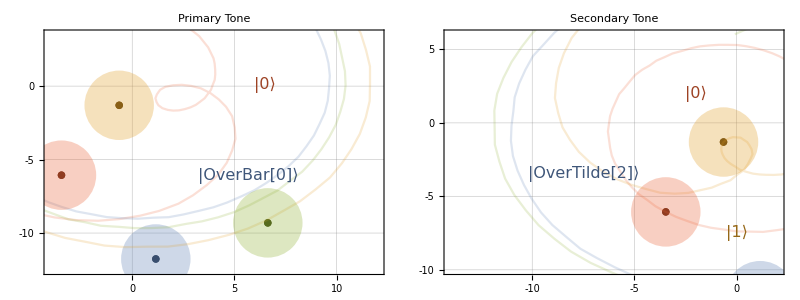
-Graphics-       Quadrature (arb. unit)In-phase (arb. unit)

```mathematica
plotAlls21=Labeled[Grid[{(*{"Primary Tone","Secondary Tone"},*){fitplot1iq,fitplot1iqef}}],{"       Quadrature (arb. unit)","In-phase (arb. unit)"},{Bottom,Left},RotateLabel->True,Frame->False,FrameMargins->1,LabelStyle->Directive[fontsize,FontFamily->font],ImageMargins->0]
```

### Readout Resonator Model

```mathematica
Clear[a,b,J]
```

```mathematica
rSol=Solve[{-I*Δrd*a-I*J*b-(γa/2)a,-I*Δfd*b-I*J*a-(κf/2)b-I*(1-Γ1)*ϵf}=={0,0},{a,b}]⟦1⟧;
```

```mathematica
modelr=20Log10[Abs[(((1-Γ2)*b/.rSol)/.{Δrd->ωr-f,Δfd->ωp-f,Γ1->1/(1+I*z1*f),Γ2->1/(1+I*z2*f)})]](*/.resultf["BestFitParameters"]⟦3;;4⟧*);
```

```mathematica
resultr2=NonlinearModelFit[r2gs,modelr,{{ωp,6.4},{κf,0.13},{ωr,ωrg⟦2⟧},{J,0.027},{γa,0.01},{ϵf,5},{z1,0.1},{z2,0.1}},f,MaxIterations->1000];
resultr2e=NonlinearModelFit[r2es,modelr,{{ωp,6.4},{κf,0.13},{ωr,ωre⟦2⟧},{J,0.027},{γa,0.001},{ϵf,5},{z1,0.1},{z2,0.1}},f,MaxIterations->1000];
resultr2f=NonlinearModelFit[r2fs,modelr,{{ωp,6.4},{κf,0.13},{ωr,ωrf⟦2⟧},{J,0.027},{γa,0.001},{ϵf,5},{z1,0.1},{z2,0.1}},f,MaxIterations->1000];
resultr2h=NonlinearModelFit[r2hs,modelr,{{ωp,6.4},{κf,0.13},{ωr,ωrh⟦2⟧},{J,0.027},{γa,0.001},{ϵf,5},{z1,0.1},{z2,0.1}},f,MaxIterations->1000];
```

```mathematica
offset=35;
r2gsp=r2gs;r2gsp⟦All,2⟧=r2gs⟦All,2⟧-offset;r2esp=r2es;r2esp⟦All,2⟧=r2es⟦All,2⟧-offset;r2fsp=r2fs;r2fsp⟦All,2⟧=r2fs⟦All,2⟧-offset;r2hsp=r2hs;r2hsp⟦All,2⟧=r2hs⟦All,2⟧-offset;
```

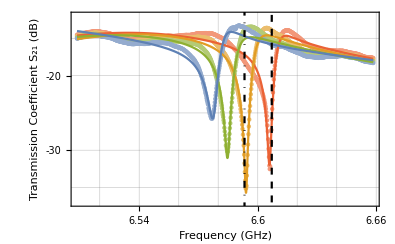

-Graphics-       Quadrature (arb. unit)In-phase (arb. unit)

```mathematica
imsize=395;
fitplot2e=Legended[Show[ListPlot[{r2gsp,r2esp,r2fsp,r2hsp},Joined->False,ImageMargins->0,ImageSize->imsize,PlotRange->{{r2sweep[[1]],r2sweep[[-1]]},{-12,-37}},GridLines->{Range[6.48,6.68,0.02],Range[-40,0,5]},Frame->True,FrameTicks->{{Range[-40,0,5],None},{Range[6.48,6.68,0.02]/. {5.->5,6.->6,7.->7,8.->8},None}},PlotStyle->Thread[{{Lighter[myred],Lighter[myorange],Lighter[mygreen],Lighter[myblue]},Table[PointSize[0.008],4]}],FrameLabel->{"Frequency (GHz)","Transmission Coefficient \!\(\*SubscriptBox[\(S\), \(21\)]\) (dB)"}],Plot[{resultr2[f]-offset,resultr2e[f]-offset,resultr2f[f]-offset,resultr2h[f]-offset},{f,r2sweep[[1]],r2sweep[[-1]]},PlotStyle->{myred,myorange,mygreen,myblue},PlotRange->All,Exclusions->None],ListPlot[{{{r2sweep[[ind]],-10},{r2sweep[[ind]],-40}},{{r2sweep[[ind1]],-10},{r2sweep[[ind1]],-40}}},Joined->True,PlotStyle->{{Black,Dashed},{Black,DotDashed}}]],{Placed[Framed[LineLegend[{myred,myorange,mygreen,myblue},{"|0⟩","|1⟩","|2⟩","|3⟩"},LabelStyle->{FontSize->fontsize-2,FontFamily->font}],Background->White,FrameMargins->0],{Right,Bottom}],Placed[Framed[LineLegend[{Directive[Black,Dashed],Directive[Black,DotDashed]},{"Primary","Secondary"},LabelStyle->{FontSize->fontsize-2,FontFamily->font}],Background->White,FrameMargins->0],{Left,Bottom}]}]
plotAlls21
```

## Single-shot Readout IQ Data

### Import IQ Data

```mathematica
dataPathIQ=dataPath<>"Single-shotReadout/";
calib1i=Flatten[Import[dataPathIQ<>"t1i_gefh_calib.csv","csv"]];
calib1q=Flatten[Import[dataPathIQ<>"t1q_gefh_calib.csv","csv"]];
calib2i=Flatten[Import[dataPathIQ<>"t2i_gefh_calib.csv","csv"]];
calib2q=Flatten[Import[dataPathIQ<>"t2q_gefh_calib.csv","csv"]];
data1i=Flatten[Import[dataPathIQ<>"t1i_gef_data.csv","csv"]];
data1q=Flatten[Import[dataPathIQ<>"t1q_gef_data.csv","csv"]];
data2i=Flatten[Import[dataPathIQ<>"t2i_gef_data.csv","csv"]];
data2q=Flatten[Import[dataPathIQ<>"t2q_gef_data.csv","csv"]];
data1ipre=Flatten[Import[dataPathIQ<>"t1i_gef_data_pre.csv","csv"]];
data1qpre=Flatten[Import[dataPathIQ<>"t1q_gef_data_pre.csv","csv"]];
data2ipre=Flatten[Import[dataPathIQ<>"t2i_gef_data_pre.csv","csv"]];
data2qpre=Flatten[Import[dataPathIQ<>"t2q_gef_data_pre.csv","csv"]];
fontsize = 20;
```

### Sample Training Data

```mathematica
calibAll={calib1i,calib1q,calib2i,calib2q}ᵀ;
dataAll={data1i,data1q,data2i,data2q}ᵀ;
preData={data1ipre,data1qpre,data2ipre,data2qpre}ᵀ;
dataLen=Dimensions[calibAll]⟦1⟧/4;
dataGpre=preData⟦1;;1*dataLen⟧;
dataEpre=preData⟦dataLen+1;;2*dataLen⟧;
dataFpre=preData⟦2*dataLen+1;;3*dataLen⟧;
dataG=dataAll⟦1;;1*dataLen⟧;
dataE=dataAll⟦dataLen+1;;2*dataLen⟧;
dataF=dataAll⟦2*dataLen+1;;3*dataLen⟧;
calibG=calibAll⟦1;;1*dataLen⟧;
calibE=calibAll⟦dataLen+1;;2*dataLen⟧;
calibF=calibAll⟦2*dataLen+1;;3*dataLen⟧;
calibH=calibAll⟦3*dataLen+1;;4*dataLen⟧;
sample=10000;
calibGSample=RandomSample[calibG,sample];
calibESample=RandomSample[calibE,sample];
calibFSample=RandomSample[calibF,sample];
calibHSample=RandomSample[calibH,sample];
```

### Plot IQ Values

#### Primary Tone

```mathematica
dataGMeant1=Mean[calibG]⟦1;;2⟧;
dataEMeant1=Mean[calibE]⟦1;;2⟧;
dataFMeant1=Mean[calibF]⟦1;;2⟧;
datat1=Mean[{dataGMeant1,dataEMeant1}];
```

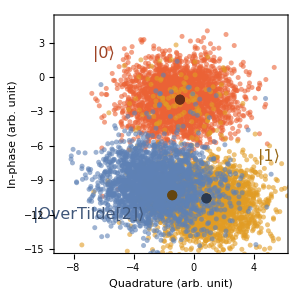

```mathematica
sample1=2500;
dataGSamplet1=RandomSample[dataG,sample1]⟦All,1;;2⟧;
dataESamplet1=RandomSample[dataE,sample1]⟦All,1;;2⟧;
dataFSamplet1=RandomSample[dataF,sample1]⟦All,1;;2⟧;
pts=0.012;opa=0.6;
is=300;
rt1=Show[ListPlot[{dataGSamplet1,dataFSamplet1,dataESamplet1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]},{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->is,PlotRange->{{-9,6},{-15,5}},Epilog->{{Text[Style["|0⟩",fontsize+2,Darker[myred]],{-6,2}]},{Text[Style["|OverTilde[2]⟩",fontsize+2,Darker[myblue]],{-7,-12}]},{Text[Style["|1⟩",fontsize+2,Darker[myorange]],{5,-7}]}}],
ListPlot[{{dataGMeant1},{dataEMeant1},{dataFMeant1}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

#### Secondary Tone

```mathematica
dataGMeant2=Mean[dataG]⟦3;;4⟧;
dataEMeant2=Mean[dataE]⟦3;;4⟧;
dataFMeant2=Mean[dataF]⟦3;;4⟧;
datat2=Mean[{dataGMeant2,dataEMeant2,dataFMeant2}];
```

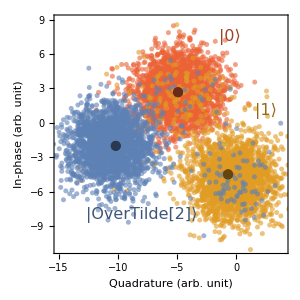

```mathematica
sample1=2500;
dataGSample1=RandomSample[dataG,sample1]⟦All,3;;4⟧;
dataESample1=RandomSample[dataE,sample1]⟦All,3;;4⟧;
dataFSample1=RandomSample[dataF,sample1]⟦All,3;;4⟧;
pts=0.012;opa=0.6;
rt2=Show[ListPlot[{dataGSample1,dataFSample1,dataESample1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]}(*,{PointSize[pts],mygreen,Opacity[opa]}*),{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->is,PlotRange->{{-15,4},{9-20,9}},Epilog->{{Text[Style["|0⟩",fontsize+2,Darker[myred]],{-0.5,7.5}]},{Text[Style["|OverTilde[2]⟩",fontsize+2,Darker[myblue]],{-8,-8}]},{Text[Style["|1⟩",fontsize+2,Darker[myorange]],{2.5,1}]}}],
ListPlot[{{dataGMeant2},{dataEMeant2},{dataFMeant2}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

## Baseline Single-tone Assignment Fidelity

```mathematica
Clear[PointerState]
PointerState[meanList_,data_]:=Module[{},distance={};
Do[AppendTo[distance,
Norm[#-meanList⟦i⟧]&/@data],{i,1,Dimensions[meanList]⟦-1⟧+1}];
count=Position[#,Min[#]]⟦1,1⟧&/@(distanceᵀ);
count]
```

### Pointer-state Classification

```mathematica
calibGMean=Mean[calibG]⟦3;;4⟧;
calibEMean=Mean[calibE]⟦3;;4⟧;
calibFMean=Mean[calibF]⟦3;;4⟧;
```

```mathematica
meanList={calibGMean,calibEMean,calibFMean};
countBase=PointerState[meanList,calibAll⟦;;-dataLen,3;;4⟧]-1;
```

### Re-construct and Plot Assignment Matrix

```mathematica
selectBase= Table[True,dataLen*3];
cmsBase=FindCM[Partition[countBase,dataLen],Partition[select,dataLen],Partition[select,dataLen],plot=True,twotone=False];
```

```mathematica
m=Round[cms⟦2⟧*100,0.01];
a=50;max=100;
cf=Opacity[1-a^(-#/max),myblue]&;
fa=Round[Mean[Diagonal[cms⟦2⟧*100]],0.01];faBase=fa;
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

```mathematica
ml=Round[cms⟦2⟧*100,100];
legendPlot=Show[MatrixPlot[ml,(*ImageMargins->{{20,0},{0,20}},*)ImageSize->{120,is},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->fontsize,FontFamily->font],Right,Rotate[#,90 Degree]&]],{1,0.5}]],MatrixPlot[ml,Epilog->Style[Text@@@Transpose[{Catenate@ml,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->is,ColorFunction->cf,ColorFunctionScaling->False]];
cm0Plot=Show[MatrixPlot[m,Epilog->MapIndexed[Text[Style[Round[#,.01],fontsize,If[Abs[#]≥50,White,Black],FontFamily->font],{#2[[2]],4-#2[[1]]}-.5]&,m,{2}],(*ImageMargins->{{20,0},{0,20}},*)FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->{is+100,is},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},(*PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->24],Right,Rotate[#,90 Degree]&]],{1,0.5}],*)FrameLabel->{ "Prepared State","Measured State","",Style["Three-state Readout\n Assignment Fidelity ℱ_a = "<>ToString[fa]<>"%",fontsize]}],MatrixPlot[m,Epilog->Style[Text@@@Transpose[{Catenate@m,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->is,ColorFunction->cf,ColorFunctionScaling->False]];
Show[cm0Plot,legendPlot]
```

-Graphics-

## Neural Network

### Train Neural Network

```mathematica
trainingData=Flatten[{#-> 0&/@calibGSample,#-> 1&/@calibESample,#-> 3&/@calibHSample}];
net=NetChain[{LinearLayer[32],ElementwiseLayer[Ramp],LinearLayer[3],SoftmaxLayer[]},"Input"->{4},"Output"->NetDecoder[{"Class",{0,1,3}}]];
Information[net,"SummaryGraphic"]
```

-Graphics-

```mathematica
results=NetTrain[net,trainingData,All]
trained=results["TrainedNet"]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12194  rounds:26  time:28s  examples/s:28234
data | ,,  training examples:30000  processed examples:780416  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.51×10^-1  error:3.26%
 | 
 | ]

NetChain[<>]

## State Discrimination

```mathematica
Clear[ThresholdData,FindCM] 
ThresholdData[countProb_,thres_]:=Module[{},gselect=(Max[#]>thres⟦1⟧)&/@(Flatten[Values[countProb⟦1⟧]]);
eselect=(Max[#]>thres⟦2⟧)&/@(Flatten[Values[countProb⟦2⟧]]);
fselect=(Max[#]>thres⟦3⟧)&/@(Flatten[Values[countProb⟦3⟧]]);
{gselect,eselect,fselect}]
FindCM[count_,select_,preselect_,plot_:False,twotone_:True]:=Module[{},gselectFinal=Thread[And[select⟦1⟧,preselect⟦1⟧]];
eselectFinal=Thread[And[select⟦2⟧,preselect⟦2⟧]];
fselectFinal=Thread[And[select⟦3⟧,preselect⟦3⟧]];
gcountFinal=Pick[count⟦1⟧,gselectFinal];ecountFinal=Pick[count⟦2⟧,eselectFinal];fcountFinal=Pick[count⟦3⟧,fselectFinal];
If[twotone,
cag=Flatten[Count[gcountFinal,#](*/Dimensions[gcountFinal]*)&/@{0,1,2,3}];
cag=cag⟦1;;2⟧~Join~{Total[cag⟦3;;4⟧]}//N;
cae=Flatten[Count[ecountFinal,#](*/Dimensions[ecountFinal]*)&/@{0,1,2,3}];
cae={cae⟦1⟧}~Join~{Total[cae⟦3;;4⟧]}~Join~{cae⟦2⟧}//N;
caf=Flatten[Count[fcountFinal,#](*/Dimensions[fcountFinal]*)&/@{0,1,2,3}];
caf={caf⟦1⟧}~Join~{Total[caf⟦3;;4⟧]}~Join~{caf⟦2⟧}//N;
,
cag=Flatten[Count[gcountFinal,#](*/Dimensions[gcountFinal]*)&/@{0,1,2}];
cae=Flatten[Count[ecountFinal,#](*/Dimensions[ecountFinal]*)&/@{0,1,2}];
caf=Flatten[Count[fcountFinal,#](*/Dimensions[fcountFinal]*)&/@{0,1,2}];];
cm={cag,cae,caf};
cmNorm={cag/Dimensions[gcountFinal]⟦1⟧,cae/Dimensions[ecountFinal]⟦1⟧,caf/Dimensions[fcountFinal]⟦1⟧};
(*If[plot,
Print[Mean[Diagonal[cm]],cm//MatrixForm,Mean[Diagonal[cmNorm]],cmNorm//MatrixForm]];*)
{cm,cmNorm}]
```

### Preselection

```mathematica
c=trained;
gprecountProb=c[dataGpre,"Probabilities"];
eprecountProb=c[dataEpre,"Probabilities"];
fprecountProb=c[dataFpre,"Probabilities"];
```

```mathematica
threspre=0.5;
gpreselect=(#>threspre)&/@(0/.gprecountProb);
epreselect=(#>threspre)&/@(0/.eprecountProb);
fpreselect=(#>threspre)&/@(0/.fprecountProb);
preselect={gpreselect,epreselect,fpreselect};
```

### Classification

```mathematica
gcountProb=MaximalBy[1]@# &/@c[dataG,"Probabilities"];
ecountProb=MaximalBy[1]@# &/@c[dataE,"Probabilities"];
fcountProb=MaximalBy[1]@# &/@c[dataF,"Probabilities"];
gcount=Flatten[Keys[gcountProb]];ecount=Flatten[Keys[ecountProb]];fcount=Flatten[Keys[fcountProb]];
countProb ={gcountProb,ecountProb,fcountProb};
count = {gcount,ecount,fcount};
```

### Optimize Confidence Thresholds

```mathematica
thresSweep=Range[0.8,0.99,0.005];
cmList={};cmfList={};
Do[thres=thresSweep⟦i⟧;
select=ThresholdData[countProb,Table[thres,3]];
cms=FindCM[count,select,preselect];
AppendTo[cmList,cms⟦1⟧];
AppendTo[cmfList,cms⟦2⟧];
,{i,1,Dimensions[thresSweep]⟦1⟧}]
```

```mathematica
cmPlotList={};thresList={};cutoff=0.9;
Do[cmMax=Max[#]&/@(cmList⟦All,i⟧ᵀ);
cmPlot={Table[thresSweep,3],cmList⟦All,i⟧ᵀ/cmMax}ᵀ;
cmPlot=#ᵀ&/@cmPlot;cmPlot⟦i⟧;
thresIdx=Nearest[cmPlot⟦i⟧⟦All,2⟧-> "Index",cutoff];
thresPt=thresSweep⟦thresIdx⟦1⟧⟧;
AppendTo[cmPlotList,cmPlot];AppendTo[thresList,thresPt];
(*Print[ListPlot[cmPlot,Joined->True,PlotRange-> {0.7,1}]];*)
,{i,1,3}]
```

### Re-construct Assignment Matrix

```mathematica
select=ThresholdData[countProb,thresList];
cms=FindCM[count,select,preselect,plot=True];
```

```mathematica
m=Round[cms⟦2⟧*100,0.01];
a=50;max=100;
cf=Opacity[1-a^(-#/max),myblue]&;
fa=Round[Mean[Diagonal[cms⟦2⟧*100]],0.01];
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

```mathematica
ml=Round[cms⟦2⟧*100,100];is=270;
legendPlot=Show[MatrixPlot[ml,(*ImageMargins->{{20,0},{0,20}},*)ImageSize->{120,is},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->fontsize,FontFamily->font],Right,Rotate[#,90 Degree]&]],{1,0.5}]],MatrixPlot[ml,Epilog->Style[Text@@@Transpose[{Catenate@ml,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->is,ColorFunction->cf,ColorFunctionScaling->False]];
cm0Plot=Show[MatrixPlot[m,Epilog->MapIndexed[Text[Style[Round[#,.01],fontsize,If[Abs[#]≥50,White,Black],FontFamily->font],{#2[[2]],4-#2[[1]]}-.5]&,m,{2}],(*ImageMargins->{{20,0},{0,20}},*)FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->{is+100,is},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},(*PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->24],Right,Rotate[#,90 Degree]&]],{1,0.5}],*)FrameLabel->{ "Prepared State","Measured State","",Style["Three-state Readout\n Assignment Fidelity ℱ_a = "<>ToString[fa]<>"%",fontsize]}],MatrixPlot[m,Epilog->Style[Text@@@Transpose[{Catenate@m,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->is,ColorFunction->cf,ColorFunctionScaling->False]];
Show[cm0Plot,legendPlot]
```

-Graphics-

### Plot Decision Boundary

#### Primary Tone

```mathematica
x1=-9;x2=6;y1=-15;y2=5;
xy1=Table[{i,j},{i,x1,x2},{j,y1,y2}];
d=Dimensions[xy1];
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{1->1,2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
dbt1=Show[cp11,cp41];
```

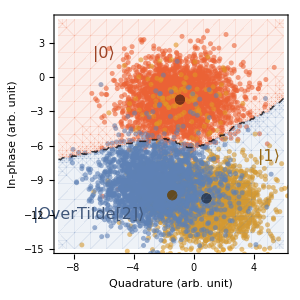

```mathematica
Show[rt1,dbt1]
```

#### Secondary Tone

```mathematica
x1=-20;x2=5;y1=-15;y2=10;
xy1=Table[{i,j},{i,x1,x2},{j,y1,y2}];
d=Dimensions[xy1];
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myorange,Opacity[0.1]],1≤x<2}}]
cp21=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->0,3->0},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{1->0,2->0,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
dbt2=Show[cp11,cp21,cp41];
```

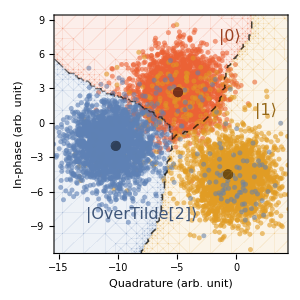

```mathematica
Show[rt2,dbt2]
```